```mathematica
(* Calculate 5 factorial and only use commands of a counter mashine: *)
list={0,5}~Join~Table[0,{10}]
Do[
Label[begin2];If[list[[1]]==0,Goto[end2]];list[[1]]--;Pause[0.05];Goto[begin2];Label[end2];list[[1]]++;Pause[0.05];Label[begin4];If[list[[7]]==0,Goto[end4]];list[[7]]--;Pause[0.05];Goto[begin4];Label[end4];Label[begin6];If[list[[2]]==0,Goto[end6]];list[[2]]--;Pause[0.05];list[[7]]++;Pause[0.05];list[[4]]++;Pause[0.05];Goto[begin6];Label[end6];Label[begin7];If[list[[4]]==0,Goto[end7]];list[[4]]--;Pause[0.05];list[[2]]++;Pause[0.05];Goto[begin7];Label[end7];If[list[[7]]==0,Goto[end0]];Label[begin0];Label[begin11];If[list[[5]]==0,Goto[end11]];list[[5]]--;Pause[0.05];Goto[begin11];Label[end11];Label[begin13];If[list[[7]]==0,Goto[end13]];list[[7]]--;Pause[0.05];list[[5]]++;Pause[0.05];list[[4]]++;Pause[0.05];Goto[begin13];Label[end13];Label[begin14];If[list[[4]]==0,Goto[end14]];list[[4]]--;Pause[0.05];list[[7]]++;Pause[0.05];Goto[begin14];Label[end14];Label[begin9];If[list[[7]]==0,Goto[end9]];list[[7]]--;Pause[0.05];Label[begin16];If[list[[1]]==0,Goto[end16]];list[[1]]--;Pause[0.05];list[[6]]++;Pause[0.05];list[[4]]++;Pause[0.05];Goto[begin16];Label[end16];Label[begin17];If[list[[4]]==0,Goto[end17]];list[[4]]--;Pause[0.05];list[[1]]++;Pause[0.05];Goto[begin17];Label[end17];Goto[begin9];Label[end9];Label[begin18];If[list[[5]]==0,Goto[end18]];list[[5]]--;Pause[0.05];list[[7]]++;Pause[0.05];Goto[begin18];Label[end18];Label[begin20];If[list[[1]]==0,Goto[end20]];list[[1]]--;Pause[0.05];Goto[begin20];Label[end20];Label[begin22];If[list[[6]]==0,Goto[end22]];list[[6]]--;Pause[0.05];list[[1]]++;Pause[0.05];list[[4]]++;Pause[0.05];Goto[begin22];Label[end22];Label[begin23];If[list[[4]]==0,Goto[end23]];list[[4]]--;Pause[0.05];list[[6]]++;Pause[0.05];Goto[begin23];Label[end23];Label[begin24];If[list[[6]]==0,Goto[end24]];list[[6]]--;Pause[0.05];Goto[begin24];Label[end24];list[[7]]--;Pause[0.05];If[list[[7]]==0,Goto[end0]];Goto[begin0];Label[end0];Label[begin25];If[list[[7]]==0,Goto[end25]];list[[7]]--;Pause[0.05];Goto[begin25];Label[end25],
{1}
]
list
```

{0,3,0,0,0,0,0,0,0,0,0,0}

{6,3,0,0,0,0,0,0,0,0,0,0}

```mathematica
Dynamic[list]
```

```mathematica
(*Since nobody wants to write Code for Counter machines, this program does it for us by iteratively replacing complicated strings by easier ones.*)
(* The operation in string is converted to counter mashine commands. Copy paste these commands into the "Do"-Command above to see the execution. *)
string="list[[3]]=list[[1]]^list[[2]];";
string="list[[1]]=list[[2]]!;";
(*string="If[list[[1]]==list[[2]],Goto[3]];";*)


x=0;
While[x<100,
newstring=StringReplace[string,
{

(* EqualTest 
RegularExpression["If\[list\[\[(.)\]\]>=list\[\[(.)\]\],Goto\[(.)\]\];"]->StringJoin["$1, $2, $3"],*)

(*Factorial*)
RegularExpression["list\[\[(.)\]\]=list\[\[(.)\]\]!;"]->StringJoin["list[[$1]]=1;list[[7]]=list[[$2]];If[list[[7]]==0,Goto[end",ToString[x],"]];Label[begin",ToString[x],"];list[[$1]]*=list[[7]];list[[7]]--;If[list[[7]]==0,Goto[end",ToString[x],"]];Goto[begin",ToString[x],"];Label[end",ToString[x],"];list[[7]]=0;"],

(*Power*)
RegularExpression["list\[\[(.)\]\]=list\[\[(.)\]\]\\^list\[\[(.)\]\];"]->StringJoin["list[[7]]=list[[$3]];list[[$1]]=1;Label[begin",ToString[x],"];If[list[[$3]]==0,Goto[end",ToString[x],"]];list[[$3]]--;list[[$1]]*=list[[$2]];Goto[begin",ToString[x],"];Label[end",ToString[x],"];DRAIN(7,$3);"],

(* * *)
RegularExpression["list\[\[(.)\]\]=list\[\[(.)\]\]list\[\[(.)\]\];"]->StringJoin["list[[5]]=list[[$3]];Label[begin", ToString[x],"];If[list[[$3]]==0,Goto[end", ToString[x],"]];list[[$3]]--;list[[$1]]+=list[[$2]];Goto[begin", ToString[x],"];Label[end", ToString[x],"];DRAIN(5,$3);"],

(*DRAIN: Addiert $1 auf $2 und löscht $1. *)
RegularExpression["DRAIN\\((.),(.)\\);"]->StringJoin["Label[begin", ToString[x],"];If[list[[$1]]==0,Goto[end", ToString[x],"]];list[[$1]]--;list[[$2]]++;Goto[begin", ToString[x],"];Label[end", ToString[x],"];"],

(*DRAIN 2: Addiert $1 und $2 UND $3 und löscht $1. *)
RegularExpression["DRAIN\\((.),(.),(.)\\);"]->StringJoin["Label[begin", ToString[x],"];If[list[[$1]]==0,Goto[end", ToString[x],"]];list[[$1]]--;list[[$2]]++;list[[$3]]++;Goto[begin", ToString[x],"];Label[end", ToString[x],"];"],

(* *= *)
RegularExpression["list\[\[(.)\]\]\\*=list\[\[(.)\]\];"]->StringJoin["list[[6]]=list[[$1]]list[[$2]];list[[$1]]=list[[6]];list[[6]]=0;"],

(* = *)
RegularExpression["list\[\[(.)\]\]=list\[\[(.)\]\];"]->StringJoin["list[[$1]]=0;list[[$1]]+=list[[$2]];"],

(* += *)
RegularExpression["list\[\[(.)\]\]\\+=list\[\[(.)\]\];"]->StringJoin["DRAIN($2,$1,4);DRAIN(4,$2);"],

(* =1 *)
RegularExpression["list\[\[(.)\]\]=1;"]->StringJoin["list[[$1]]=0;list[[$1]]++;"],

(* =0 *)
RegularExpression["list\[\[(.)\]\]=0;"]->StringJoin["Label[begin", ToString[x],"];If[list[[$1]]==0,Goto[end", ToString[x],"]];list[[$1]]--;Goto[begin", ToString[x],"];Label[end", ToString[x],"];"]


},1
];
If[SameQ[newstring,string],Break[],string=newstring];
x++
]
(* This inserts a Pause after each incement or decrement s.t. one can nicely watch the calculation with Dynamic *)
string=StringReplace[string,
{
RegularExpression["list\[\[(.)\]\](\\+\\+|--);"]->"list[[$1]]$2;Pause[0.05];"
}
]
x
```

Label[begin2];If[list[[1]]==0,Goto[end2]];list[[1]]--;Pause[0.05];Goto[begin2];Label[end2];list[[1]]++;Pause[0.05];Label[begin4];If[list[[7]]==0,Goto[end4]];list[[7]]--;Pause[0.05];Goto[begin4];Label[end4];Label[begin6];If[list[[2]]==0,Goto[end6]];list[[2]]--;Pause[0.05];list[[7]]++;Pause[0.05];list[[4]]++;Pause[0.05];Goto[begin6];Label[end6];Label[begin7];If[list[[4]]==0,Goto[end7]];list[[4]]--;Pause[0.05];list[[2]]++;Pause[0.05];Goto[begin7];Label[end7];If[list[[7]]==0,Goto[end0]];Label[begin0];Label[begin11];If[list[[5]]==0,Goto[end11]];list[[5]]--;Pause[0.05];Goto[begin11];Label[end11];Label[begin13];If[list[[7]]==0,Goto[end13]];list[[7]]--;Pause[0.05];list[[5]]++;Pause[0.05];list[[4]]++;Pause[0.05];Goto[begin13];Label[end13];Label[begin14];If[list[[4]]==0,Goto[end14]];list[[4]]--;Pause[0.05];list[[7]]++;Pause[0.05];Goto[begin14];Label[end14];Label[begin9];If[list[[7]]==0,Goto[end9]];list[[7]]--;Pause[0.05];Label[begin16];If[list[[1]]==0,Goto[end16]];list[[1]]--;Pause[0.05];list[[6]]++;Pause[0.05];list[[4]]++;Pause[0.05];Goto[begin16];Label[end16];Label[begin17];If[list[[4]]==0,Goto[end17]];list[[4]]--;Pause[0.05];list[[1]]++;Pause[0.05];Goto[begin17];Label[end17];Goto[begin9];Label[end9];Label[begin18];If[list[[5]]==0,Goto[end18]];list[[5]]--;Pause[0.05];list[[7]]++;Pause[0.05];Goto[begin18];Label[end18];Label[begin20];If[list[[1]]==0,Goto[end20]];list[[1]]--;Pause[0.05];Goto[begin20];Label[end20];Label[begin22];If[list[[6]]==0,Goto[end22]];list[[6]]--;Pause[0.05];list[[1]]++;Pause[0.05];list[[4]]++;Pause[0.05];Goto[begin22];Label[end22];Label[begin23];If[list[[4]]==0,Goto[end23]];list[[4]]--;Pause[0.05];list[[6]]++;Pause[0.05];Goto[begin23];Label[end23];Label[begin24];If[list[[6]]==0,Goto[end24]];list[[6]]--;Pause[0.05];Goto[begin24];Label[end24];list[[7]]--;Pause[0.05];If[list[[7]]==0,Goto[end0]];Goto[begin0];Label[end0];Label[begin25];If[list[[7]]==0,Goto[end25]];list[[7]]--;Pause[0.05];Goto[begin25];Label[end25];

26

```mathematica
(*
Placeholders:
3: Result
4: PlusEqual
5: Times
6: TimesEqual
7: Power and Factorial
*)
```

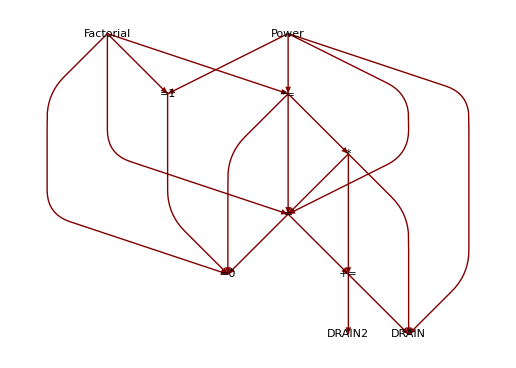

```mathematica
(* Care must be taken not to create circles in the dependancy graph. Also the placeholder of a function must be different from all placeholders of functions that it depends on. *)
LayeredGraphPlot[{"Factorial"->"=1","Factorial"->"=0","Factorial"->"*=","Factorial"->"=", "*="->"=","*="->"*","*="->"=0","Power"->"=1","Power"->"*=","Power"->"=","Power"->"DRAIN","*"->"=","*"->"+=","*"->"DRAIN","="->"=0","="->"+=","+="->"DRAIN","+="->"DRAIN2","=1"->"=0"},VertexLabeling->True]
```

```mathematica
(* Next step: Be able to do If[list[[1]]==0, COMMAND] or even If[CONDITION , COMMAND] *)
```